```mathematica
μm=10^-6;
c=299792458;
fs=10^-15;
mm=10^-3;
nm=10^-9;
```

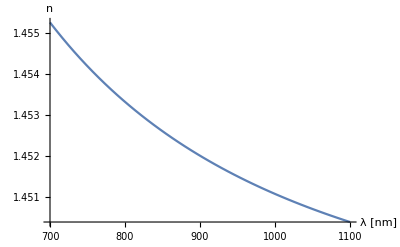

```mathematica
(*Refractive index. Ref: refractiveindex.info*)
nfs[λ_]:=1.447193+(383343.3 10^-8)/(λ/μm)^2+(5.661342 10^-5)/(λ/μm)^4(*fused silica matching liquid*)
Plot[nfs[λ nm],{λ,700,1100},AxesLabel->{"λ [nm]","n"}]
```

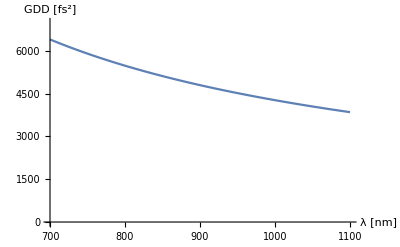

```mathematica
(*Group velocity dispersion (GVD). Ref: Young 2015 and Newport website*)
GVDfs[λ_]:=(λ^3 nfs''[λ])/(2π c^2)
(*Group delay dispersion (GDD = GVD*L, where L is the material thickness) vs wavelength*)
GDDfs[L_,λ_]:=L*GVDfs[λ]
Plot[GDDfs[100mm,λ nm]/fs^2,{λ,700,1100},PlotRange->{0,7000},AxesLabel->{"λ [nm]","GDD [fs^2]"}]
```

```mathematica
Δtout[Δt_,GDD_]:=(√(Δt^4+16 Log[2]^2 GDD^2))/Δt(*Gaussian pulse broadening*)
(*Ref: Eq8 in http://www.newport.com/The-Effect-of-Dispersion-on-Ultrashort-Pulses/602091/1033/content.aspx*)
```

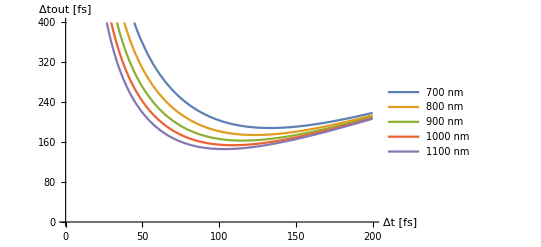

```mathematica
(*output pulsewidth vs input pulsewidth, gaussian pulses*)
Plot[Evaluate[Table[Δtout[Δt fs,GDDfs[100mm,λ nm]]/fs,{λ,700,1100,100}]],{Δt,0,200},PlotRange->{0,400},AxesLabel->{"Δt [fs]","Δtout [fs]"},PlotLegends->{"700 nm","800 nm","900 nm","1000 nm","1100 nm"}]
```

```mathematica
Δtout[55 fs,GDDfs[100mm,700 nm]]/fs
```

327.441